# The Metric Tensor

Fix a base point p and a scale r.

The pencil T_(p,r)G is the set of all germs at p: the geodesic chains γ==(x_0,x_1,…,x_r) with x_0==p. We identify it with the tangent space of the infra-observer at that point and scale.

For two germs γ,γ' the infra metric tensor g_r(γ,γ') is the parameter at which γ comes closest to the endpoint of γ', averaged over ties and divided by r.

In the plane this is the cosine of the angle between the two directions, cut off at zero.

Does the tensor converge to the metric tensor of the plane on graph approximations of it: the regular tilings under growing radius, irregular meshes under refinement?

## Setup

```mathematica
Needs["WolframInstitute`InfraGeometry`"]
```

The pencil: every germ of length r at p, as a vertex list, read off the geodesic spray graph.

```mathematica
pencil[g_, p_, r_] := With[{spray = SprayGraph[g, p]}, Join @@ Map[FindPath[spray, p, #, {r}, All] &, FindInfraShell[g, p, r]]]
```

The tensor as the table over germs and shell vertices; the tied parameters are reduced by the selector.

```mathematica
germTensor[g_, p_, r_, select_ : Mean] := With[
  {d = GraphDistanceMatrix @ g, shell = FindInfraShell[g, p, r]},
  {toShell = d[[All, VertexIndex[g, #] & /@ shell]]},
  Map[germ |-> Map[alongGerm |-> select @ Pick[Range[0, r], alongGerm, Min @ alongGerm], Transpose @ toShell[[VertexIndex[g, #] & /@ germ]]], pencil[g, p, r]] / N[r]]
```

The multiplicity of a shell vertex: the number of germs ending there.

```mathematica
germMultiplicity[g_, p_, r_] := Lookup[Counts[Last /@ pencil[g, p, r]], FindInfraShell[g, p, r]]
```

## The pencil at a point

Given p∈V(G) and a scale r, the tangent space T_(p,r)G is the pencil: the germs at p, the geodesic chains of length r from p.

Its compact representation is the geodesic spray graph, whose paths from p are exactly the geodesics from p.

Each picture below is one substrate at one size: the rows are the sizes small, medium and large, the columns the square tiling, the triangular tiling and an irregular square mesh. The base is a centre of the graph, the scale half its radius.

The spray graph of the ball B(p,r): its directed edges drawn bent, in red, on the edges of the substrate.

```mathematica
GraphicsGrid @ Table[
  With[
    {g = (SeedRandom[2]; InfraSubstrate[name, size])},
    {p = First @ GraphCenter @ g},
    {r = Floor[GraphRadius[g]/2]},
    {spray = Subgraph[SprayGraph[g, p], FindInfraRepresentative[g, InfraBall[p, r]]]},
    Graph[g, EdgeShapeFunction -> Map[e |-> (UndirectedEdge @@ e) -> With[{u = First @ e},
        Function[{points, edge}, With[{q = If[First @ edge === u, points, Reverse @ points]},
          {Line[points], StandardRed, Opacity[1], Arrowheads[Small], Arrow @ BezierCurve[{q[[1]], Mean[q] + 0.2 Cross[q[[2]] - q[[1]]], q[[2]]}]}]]],
      EdgeList @ spray]]],
  {size, {"Small", "Medium", "Large"}},
  {name, {"SquareTilingGraph", "TriangularTilingGraph", "SquareMeshGraph"}}]
```

-Graphics-

## The projection parameter

For a germ γ==(x_0,…,x_r) and a germ γ' with endpoint v,

g_r(γ,γ')==1/r mean{ k:d(x_k,v)==min_j d(x_j,v) }

The mean runs over the tied feet; the least and the greatest tied parameter give variant tensors, compared at the end.

In the plane g_r(γ,γ')==max(cosθ,0) with θ the angle between the two directions, so the entry is dimensionless and lives in [0,1].

The entry depends on γ' only through its endpoint v, so the tensor is the table over germs and shell vertices, each shell vertex counted with the number of germs ending there.

The paclet's InfraMetricTensorpaclet:WolframInstitute/InfraGeometry/ref/InfraMetricTensorWolframInstitute/InfraGeometry Package Symbol is the interval form of the same table: the foot of v is taken on the whole interval I(p,w) instead of on one germ.

One entry. The germ is red, the base and v blue, the feet and a shortest path from v to a foot orange; v is the shell vertex whose entry lies nearest the middle of the range.

```mathematica
GraphicsGrid @ Table[
  With[
    {g = (SeedRandom[2]; InfraSubstrate[name, size])},
    {p = First @ GraphCenter @ g, d = GraphDistanceMatrix @ g},
    {r = Floor[GraphRadius[g]/2]},
    {shell = FindInfraShell[g, p, r]},
    {germ = First @ pencil[g, p, r]},
    {parameter = Map[end |-> With[{alongGerm = d[[VertexIndex[g, end], VertexIndex[g, #] & /@ germ]]}, Mean @ Pick[Range[0, r], alongGerm, Min @ alongGerm]], shell] / N[r]},
    {probe = shell[[First @ Ordering[Abs[parameter - 1/2], 1]]]},
    {alongGerm = d[[VertexIndex[g, probe], VertexIndex[g, #] & /@ germ]]},
    {feet = Pick[germ, alongGerm, Min @ alongGerm]},
    InfraSubstrateHighlight[g, {
      shell -> StandardGray,
      InfraWalk[germ] -> StandardRed,
      InfraWalk[FindInfraSegment[g, probe, First @ feet]] -> StandardOrange,
      feet -> StandardOrange,
      {probe, p} -> StandardBlue}]],
  {size, {"Small", "Medium", "Large"}},
  {name, {"SquareTilingGraph", "TriangularTilingGraph", "SquareMeshGraph"}}]
```

-Graphics-

## One germ against the pencil

One germ against all others: the colour runs along the germ from the base (blue) to its end (red), and every shell vertex takes the colour of the parameter at which the germ comes closest to it.

```mathematica
GraphicsGrid @ Table[
  With[
    {g = (SeedRandom[2]; InfraSubstrate[name, size])},
    {p = First @ GraphCenter @ g, d = GraphDistanceMatrix @ g},
    {r = Floor[GraphRadius[g]/2]},
    {shell = FindInfraShell[g, p, r]},
    {germ = First @ pencil[g, p, r]},
    {parameter = AssociationThread[shell, Map[end |-> With[{alongGerm = d[[VertexIndex[g, end], VertexIndex[g, #] & /@ germ]]}, Mean @ Pick[Range[0, r], alongGerm, Min @ alongGerm]], shell] / N[r]]},
    {colour = t |-> Blend[{StandardBlue, StandardYellow, StandardRed}, t]},
    InfraSubstrateHighlight[g, Join[
      Table[InfraWalk[germ[[k ;; k + 1]]] -> colour[k/r], {k, r}],
      Map[e |-> InfraWalk[List @@ e] -> colour[Mean[parameter /@ List @@ e]], Select[EdgeList @ g, SubsetQ[shell, List @@ #] &]],
      KeyValueMap[{t, vs} |-> vs -> colour[t], GroupBy[shell, parameter]],
      {{p} -> colour[0]}]]],
  {size, {"Small", "Medium", "Large"}},
  {name, {"SquareTilingGraph", "TriangularTilingGraph", "SquareMeshGraph"}}]
```

-Graphics-

## The tensor as a matrix

A matrix needs a linear order on the pencil, and the graph offers none.

Here, and only here, the embedding is kept: the germs are ordered counterclockwise by their endpoints, the columns are the shell vertices in the same order.

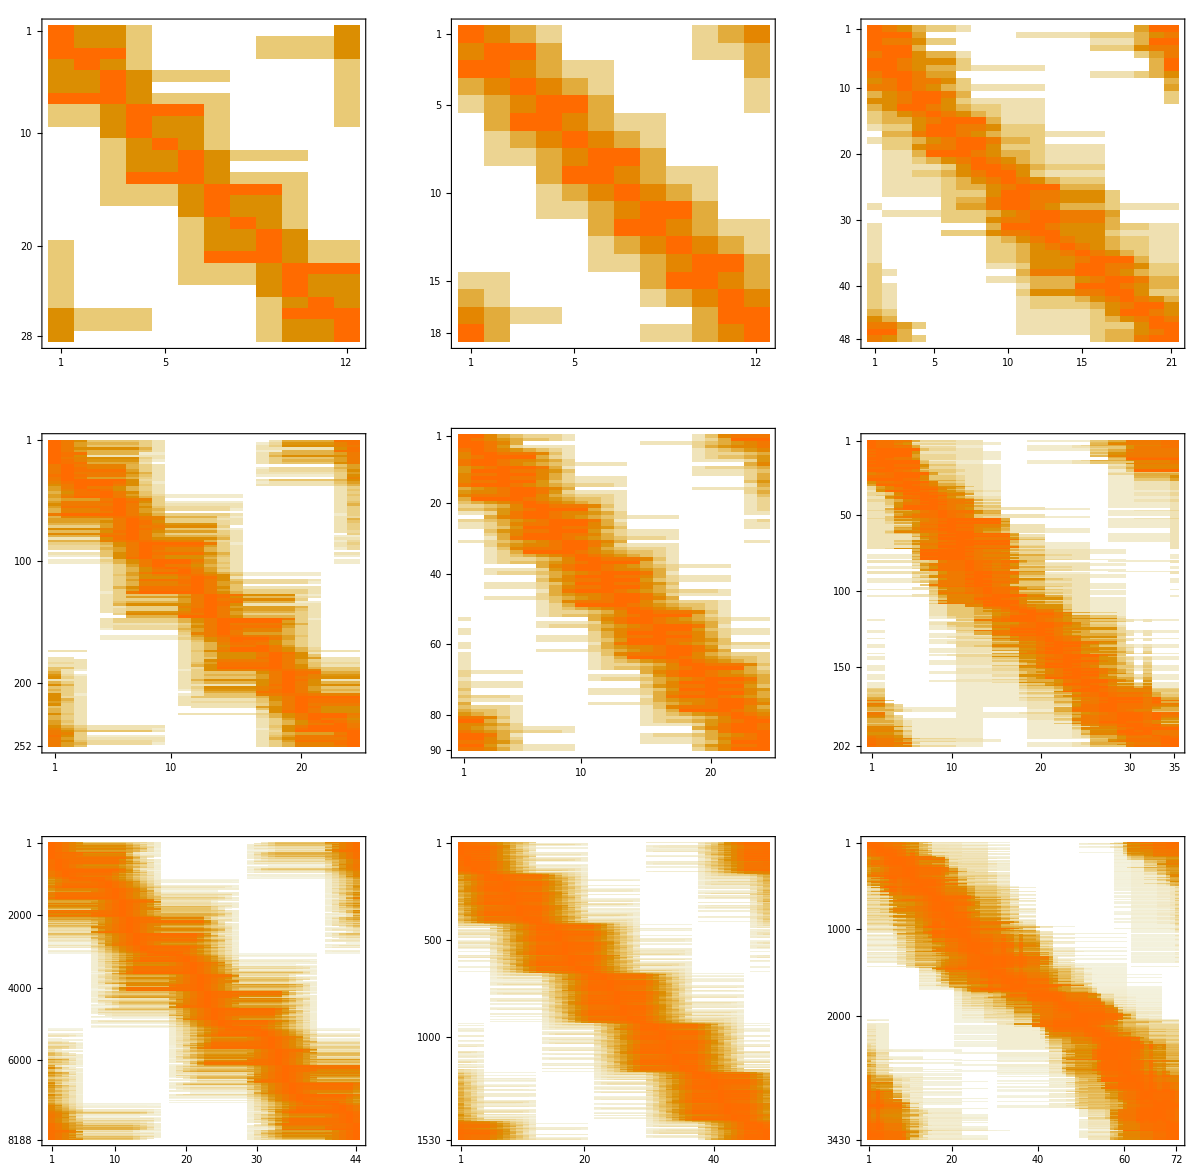

```mathematica
GraphicsGrid @ Table[
  With[
    {g = (SeedRandom[2]; InfraSubstrate[name, size, "KeepCoordinates" -> True])},
    {p = First @ GraphCenter @ g, d = GraphDistanceMatrix @ g},
    {r = Floor[GraphRadius[g]/2], coordinates = AssociationThread[VertexList @ g, GraphEmbedding @ g]},
    {angle = end |-> Mod[ArcTan @@ (coordinates[end] - coordinates[p]), 2 Pi]},
    {shell = SortBy[FindInfraShell[g, p, r], angle]},
    {germs = SortBy[pencil[g, p, r], germ |-> {angle[Last @ germ], angle[germ[[Ceiling[(r + 1)/2]]]]}]},
    {toShell = d[[All, VertexIndex[g, #] & /@ shell]]},
    MatrixPlot[Map[germ |-> Map[alongGerm |-> Mean @ Pick[Range[0, r], alongGerm, Min @ alongGerm], Transpose @ toShell[[VertexIndex[g, #] & /@ germ]]], germs] / N[r], AspectRatio -> 1]],
  {size, {"Small", "Medium", "Large"}},
  {name, {"SquareTilingGraph", "TriangularTilingGraph", "SquareMeshGraph"}}]
```

Ones on the diagonal, then parallel bands corresponding to the angle.

From the right angle on the entry is zero, because only positive projections are recorded.

For comparison, the tensor of the plane on the same germs and shell vertices: cosθ between the endpoint directions. The negative entries, blue, are the ones the infra tensor reads as zero.

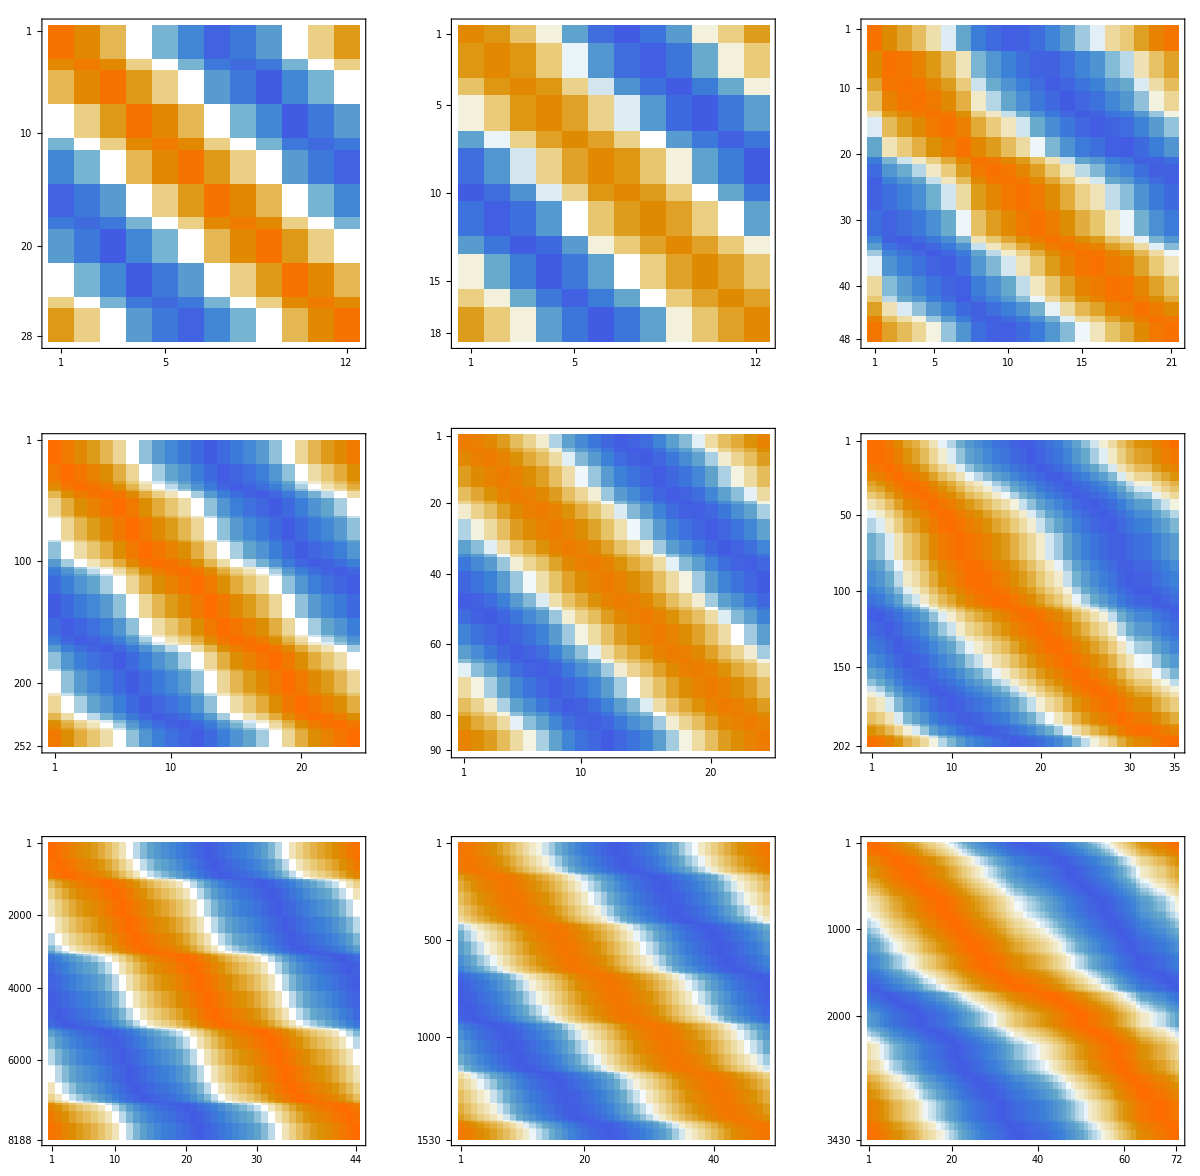

```mathematica
GraphicsGrid @ Table[
  With[
    {g = (SeedRandom[2]; InfraSubstrate[name, size, "KeepCoordinates" -> True])},
    {p = First @ GraphCenter @ g},
    {r = Floor[GraphRadius[g]/2], coordinates = AssociationThread[VertexList @ g, GraphEmbedding @ g]},
    {direction = end |-> Normalize[coordinates[end] - coordinates[p]]},
    {angle = end |-> Mod[ArcTan @@ (coordinates[end] - coordinates[p]), 2 Pi]},
    {shell = SortBy[FindInfraShell[g, p, r], angle]},
    {germs = SortBy[pencil[g, p, r], germ |-> {angle[Last @ germ], angle[germ[[Ceiling[(r + 1)/2]]]]}]},
    MatrixPlot[Outer[Dot, direction[Last @ #] & /@ germs, direction /@ shell, 1], AspectRatio -> 1]],
  {size, {"Small", "Medium", "Large"}},
  {name, {"SquareTilingGraph", "TriangularTilingGraph", "SquareMeshGraph"}}]
```

The same, cut off at zero: the smooth tensor max(cosθ,0) the infra tensor aims at.

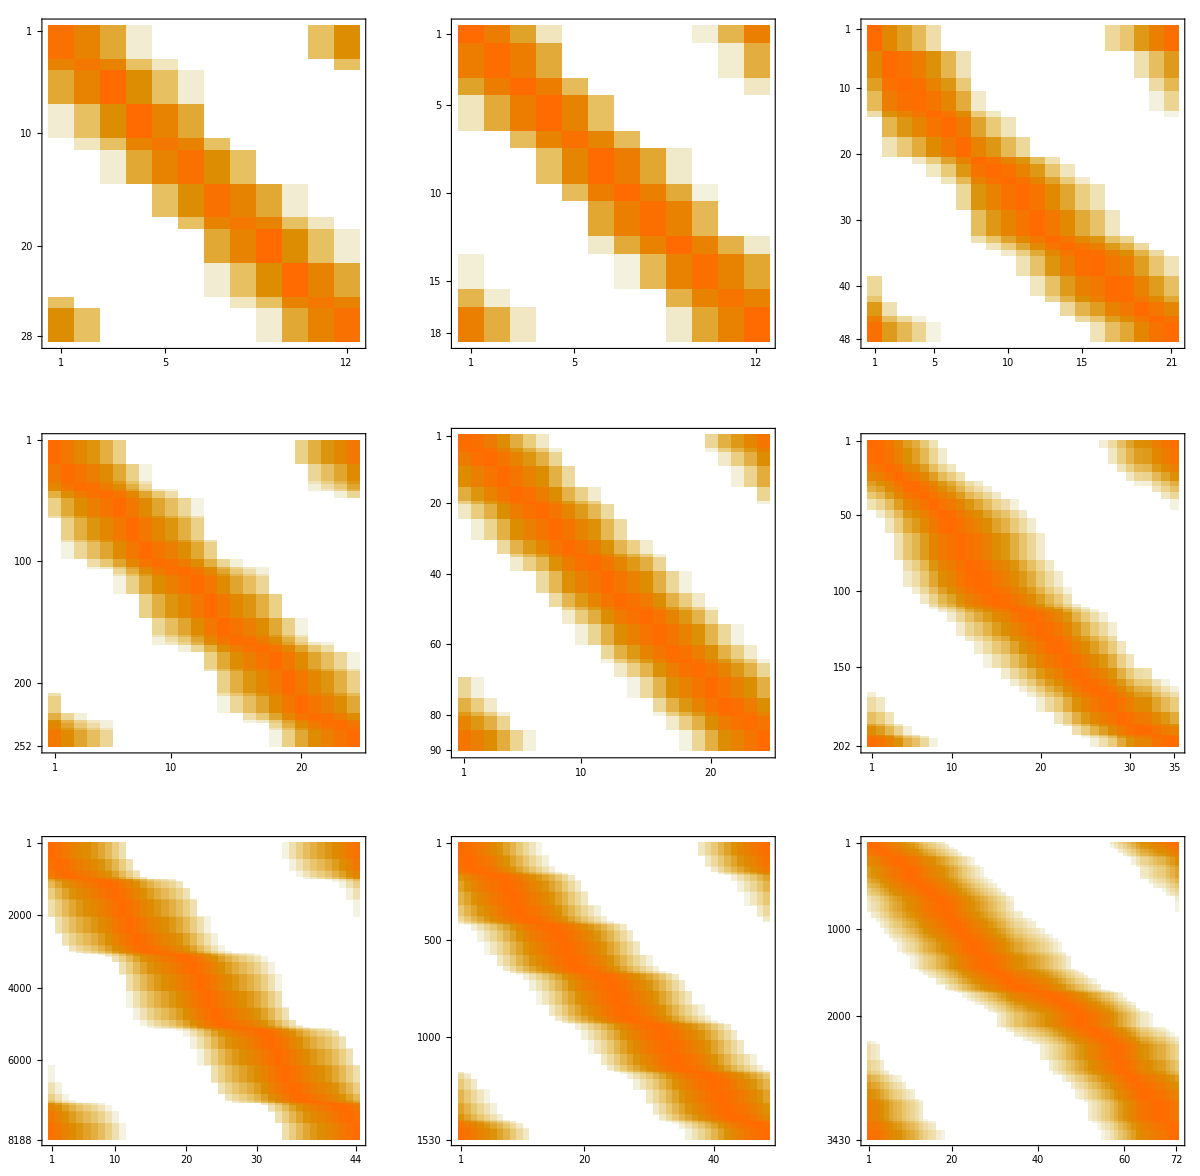

```mathematica
GraphicsGrid @ Table[
  With[
    {g = (SeedRandom[2]; InfraSubstrate[name, size, "KeepCoordinates" -> True])},
    {p = First @ GraphCenter @ g},
    {r = Floor[GraphRadius[g]/2], coordinates = AssociationThread[VertexList @ g, GraphEmbedding @ g]},
    {direction = end |-> Normalize[coordinates[end] - coordinates[p]]},
    {angle = end |-> Mod[ArcTan @@ (coordinates[end] - coordinates[p]), 2 Pi]},
    {shell = SortBy[FindInfraShell[g, p, r], angle]},
    {germs = SortBy[pencil[g, p, r], germ |-> {angle[Last @ germ], angle[germ[[Ceiling[(r + 1)/2]]]]}]},
    MatrixPlot[Clip[Outer[Dot, direction[Last @ #] & /@ germs, direction /@ shell, 1], {0, 1}], AspectRatio -> 1]],
  {size, {"Small", "Medium", "Large"}},
  {name, {"SquareTilingGraph", "TriangularTilingGraph", "SquareMeshGraph"}}]
```

## Absence of negatives and linearity

The parameter is nonnegative: a projection stops at the base and never passes it, so g_r≥0 and the tensor sees only the cosine cut off at zero.

There is no minus: no vertex of the substrate plays the negative of a direction, and linearity is a property of infinitesimal quantities with no counterpart at one fixed scale.

A candidate for the negative of a direction is the set of shell vertices at distance 2r from the chosen one: the far ends of the diameters through the base. Blue: the chosen vertex and the base. Red: the candidates. Orange: the bundle of shortest paths from the chosen vertex to them.

```mathematica
GraphicsGrid @ Table[
  With[
    {g = (SeedRandom[2]; InfraSubstrate[name, size])},
    {c = First @ GraphCenter @ g},
    {r = Floor[GraphRadius[g]/2]},
    {shell = FindInfraShell[g, c, r]},
    {u = First @ shell},
    {minus = Select[shell, GraphDistance[g, u, #] == 2 r &]},
    InfraSubstrateHighlight[g, {
      shell -> StandardGray,
      Merge[GeodesicOccupation[g, u, #] & /@ minus, Total] -> StandardOrange,
      minus -> StandardRed,
      {u, c} -> StandardBlue}]],
  {size, {"Small", "Medium", "Large"}},
  {name, {"SquareTilingGraph", "TriangularTilingGraph", "SquareMeshGraph"}}]
```

-Graphics-

The candidates form one arc opposite the chosen vertex, and every shortest path toward them crosses the base region.

## Comparing with the circle

The shell at scale r is the unit circle of the observer at that scale, and every quantity is normalized before comparison: lengths in units of r, the entries already in [0,1], the counting measure on pairs of germs over its total.

The pencil carries no cyclic order, so the tensor is compared with the cosine through its value distribution: the values g_r(γ,γ') over all pairs of germs against max(cosΘ,0) for a uniform angle Θ on [0,π], an atom of mass one half at zero.

The gap is the transport distance between the two. With F_r the distribution function of the values and F(t)==1-arccos(t)/π that of max(cosΘ,0),

gap(g_r)==∫_0^1 |F_r(t)-F(t)|ⅆt

The gap of weighted values, by the midpoint rule.

```mathematica
transportGap[values_, weights_] := With[{t = Range[0.0005, 0.9995, 0.001]},
  Mean @ Abs[CDF[EmpiricalDistribution[Flatten @ weights -> Flatten @ values], t] - (1 - ArcCos[t]/Pi)]]
```

Each substrate read at the shell of half its graph radius, against the reference.

```mathematica
GraphicsGrid @ Table[
  With[
    {g = (SeedRandom[2]; InfraSubstrate[name, size])},
    {p = First @ GraphCenter @ g},
    {r = Floor[GraphRadius[g]/2]},
    {tensor = germTensor[g, p, r], multiplicity = germMultiplicity[g, p, r]},
    Histogram[
      {WeightedData[Flatten @ tensor, Flatten @ ConstantArray[multiplicity, Length @ tensor]], Table[Max[0, Cos[Pi (k - 0.5)/2000]], {k, 2000}]},
      {0, 1, 0.05}, "PDF",
      ChartLegends -> If[{name, size} == {"SquareMeshGraph", "Large"}, Placed[{Text["tensor"], Text["reference"]}, Above], None]]],
  {size, {"Small", "Medium", "Large"}},
  {name, {"SquareTilingGraph", "TriangularTilingGraph", "SquareMeshGraph"}}]
```

-Graphics-

On the tilings the values sit on few levels: a germ is a lattice path, and the foot parameter is a lattice count.

The atom at zero is smaller than the reference's on every substrate; its missing mass sits in the first bins.

On the mesh the histogram approaches the reference as the mesh refines.

## Speed of convergence

On a tiling the base does not matter: away from the rim the graph is homogeneous, a patch of one unbounded plane, so one large graph suffices and the radius is the potential infinity. The gap is read at every radius up to half the graph radius.

The mesh has no growing radius of its own; it refines instead, read at the shell of half its graph radius.

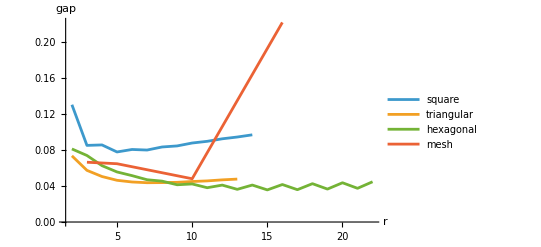

```mathematica
ListLinePlot[
  Join[
    Table[
      With[
        {g = InfraSubstrate[spec[[1]], spec[[2]]]},
        {p = First @ GraphCenter @ g},
        Table[
          With[
            {tensor = germTensor[g, p, r], multiplicity = germMultiplicity[g, p, r]},
            {r, transportGap[tensor, ConstantArray[multiplicity, Length @ tensor]]}],
          {r, 2, spec[[3]]}]],
      {spec, {{"SquareTilingGraph", 30, 14}, {"TriangularTilingGraph", 26, 13}, {"HexagonalTilingGraph", 45, 22}}}],
    {Table[
      With[
        {g = (SeedRandom[2]; InfraSubstrate["SquareMeshGraph", size])},
        {p = First @ GraphCenter @ g},
        {r = Floor[GraphRadius[g]/2]},
        {tensor = germTensor[g, p, r], multiplicity = germMultiplicity[g, p, r]},
        {r, transportGap[tensor, ConstantArray[multiplicity, Length @ tensor]]}],
      {size, {"Small", "Medium", "Large", 0.0003}}]}],
  PlotRange -> All, AxesLabel -> {Text["r"], Text["gap"]},
  PlotLegends -> Text /@ {"square", "triangular", "hexagonal", "mesh"}]
```

On the tilings the gap does not shrink: each tiling keeps its own level, and the hexagonal one alternates between two.

On the mesh it falls and then jumps at the finest refinement: the number of germs ending at a shell vertex grows unevenly along the shell, and the pair measure follows the crowded directions.

The same gap counted over pairs of a germ and a shell vertex, each shell vertex once.

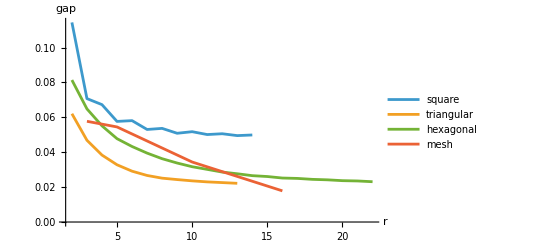

```mathematica
ListLinePlot[
  Join[
    Table[
      With[
        {g = InfraSubstrate[spec[[1]], spec[[2]]]},
        {p = First @ GraphCenter @ g},
        Table[
          With[{tensor = germTensor[g, p, r]}, {r, transportGap[tensor, ConstantArray[1, Dimensions @ tensor]]}],
          {r, 2, spec[[3]]}]],
      {spec, {{"SquareTilingGraph", 30, 14}, {"TriangularTilingGraph", 26, 13}, {"HexagonalTilingGraph", 45, 22}}}],
    {Table[
      With[
        {g = (SeedRandom[2]; InfraSubstrate["SquareMeshGraph", size])},
        {p = First @ GraphCenter @ g},
        {r = Floor[GraphRadius[g]/2]},
        {tensor = germTensor[g, p, r]},
        {r, transportGap[tensor, ConstantArray[1, Dimensions @ tensor]]}],
      {size, {"Small", "Medium", "Large", 0.0003}}]}],
  PlotRange -> All, AxesLabel -> {Text["r"], Text["gap"]},
  PlotLegends -> Text /@ {"square", "triangular", "hexagonal", "mesh"}]
```

Each tiling plateaus at its own level, the square highest.

The mesh falls throughout.

Where the feet are tied the choice of representative matters. The gaps of the least, the mean and the greatest tied parameter on the triangular tiling:

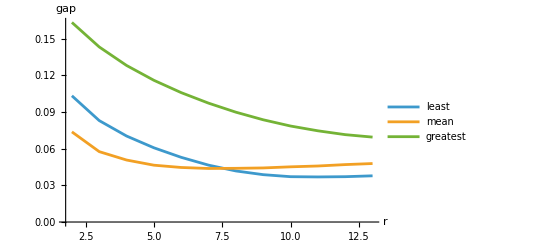

```mathematica
ListLinePlot[
  With[
    {g = InfraSubstrate["TriangularTilingGraph", 26]},
    {p = First @ GraphCenter @ g},
    {gaps = Table[
       With[
         {multiplicity = germMultiplicity[g, p, r]},
         {r, Sequence @@ Map[select |-> With[{tensor = germTensor[g, p, r, select]}, transportGap[tensor, ConstantArray[multiplicity, Length @ tensor]]], {Min, Mean, Max}]}],
       {r, 2, 13}]},
    {gaps[[All, {1, 2}]], gaps[[All, {1, 3}]], gaps[[All, {1, 4}]]}],
  PlotRange -> All, AxesLabel -> {Text["r"], Text["gap"]},
  PlotLegends -> Text /@ {"least", "mean", "greatest"}]
```

The mean is the best at small radii, the least at large radii, and the greatest the worst throughout. The mean stays the selector, as the definition says.

Related Guides

RiemannianInfrageometrypaclet:WolframInstitute/InfraGeometry/guide/RiemannianInfrageometry

Related Tech Notes

## Metadata

### Categorization

Tutorial

WolframInstitute/InfraGeometry

WolframInstitute`InfraGeometry`

WolframInstitute/InfraGeometry/tutorial/MetricTensorTutorial

### Keywords

metric tensor

tangent space

pencil

germ

geodesic

projection

cosine

convergence

tiling

mesh